John A Lewis III, 904082686, johnlewis1928@gmail.com, HW 3

Problem 1

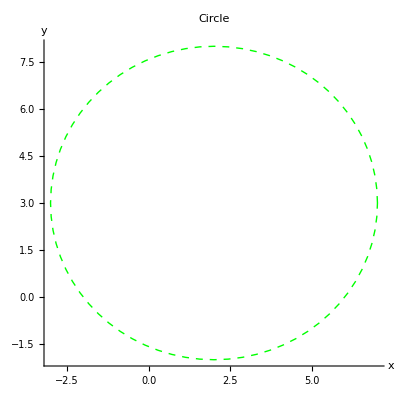

```mathematica
Quiet[Remove["Global`*"]];
Graphics[{Green,Thick,Dashed,Circle[{2,3},5]},Axes->True, PlotLabel->"Circle", AxesLabel->{"x","y"}]
```

Problem 2

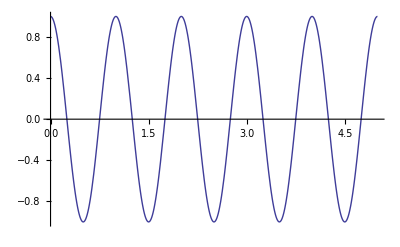

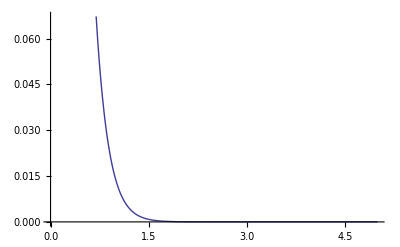

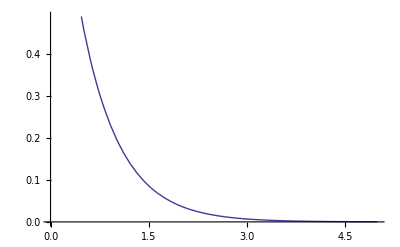

```mathematica
Remove["Global`*"];
osc[t_]:=D[x[t],t,t]+2*β*D[x[t],t] +(ω^2)*x[t];
DSolve[{osc[t]==0,x'[0]==0,x[0]==1},x[t],t] //ExpToTrig //FullSimplify;
x[t_]=x[t]/.%[[1]];
ω=2 Pi;
β=0;
Plot[Evaluate[x[t]],{t,0,5}]
Clear["β"];
Limitofx[t_]=Limit[x[t],β->2Pi];
Plot[Limitofx[t],{t,0,5}]
β=4 Pi;
Plot[Evaluate[x[t]],{t,0,5}]
```

Problem 3

```mathematica
Quiet[Remove["Global`*"]];
(*Parameter Block*)
a={A,B};elnew={el1new[t],el2new[t]};
(***************************************************************
Solving Lagrangian**********************************************)
T[t_]=.5 m1 D[x[t],t]^2 + .5 m2 D[y[t],t]^2;
V[t_]=.5 k (x[t]-y[t]-L )^2;
x[t_]=q1[t]+L;
y[t_]=q2[t];
lag[t_]:=T[t]-V[t];
elnew[[1]]=(D[lag[t],q1[t]]-Dt[D[lag[t],q1'[t]],t,Constants->{k,m1,m2,w ,A,B,L}] );
elnew[[2]]=(D[lag[t],q2[t]]-Dt[D[lag[t],q2'[t]],t,Constants->{k,m1,m2,w,A,B,L}] );
(*Guess at general solution*)
q1[t_]=a[[1]]*Exp[I w t];q2[t_]=a[[2]]*Exp[I w t];
elnew[[1]]=elnew[[1]]/(m1 Exp[I w t])  //Simplify //Expand;
elnew[[2]]=elnew[[2]]/(m2 Exp[I w t])  //Simplify //Expand;
(*Puttin equaons into a matrix form*)
element[i_,j_]:=elnew[[i]]/.a[[j]]->1/.a[[-j]]->0 //FullSimplify;
matrix=Table[element[i,j],{i,1,2},{j,1,2}] ;
Solve[Det[matrix]==0];
matrix=matrix/.%[[1]];
Solve[matrix.a==0][[1]]
```

{A→-(1. B m2)/m1}

Problem 4

True

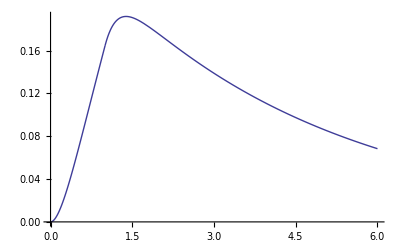

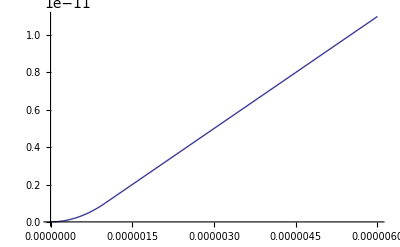

```mathematica
Remove["Global`*"];
(****Parameter Block****)
osc=x''[t]+2 β x'[t]+ω^2 x[t];
(***********************)
ℱ=Piecewise[{{a,0≤t≤τ}},0];
soln1=DSolve[{osc==a,x[0]==0,x'[0]==0},x[t],t];
xi[t_]=x[t]/.soln1[[1]];
soln2=DSolve[{osc==0,x[τ]==xi[τ],x'[τ]==xi'[τ]},x[t],t];
xf[t_]=x[t]/.soln2[[1]];
ploti:=Plot[xi[t]/c,{t,0, τ},PlotRange->All];
plotf:=Plot[xf[t]/c,{t,τ,6 τ},PlotRange->All];
(****Parameter Block****)
ω:=1;a:=1;τ:=1;
β:=Sqrt[5] ω;c:=a/ω^2;
xi[τ]==xf[τ]
(***********************)
Show[{ploti,plotf}]
(****Parameter Block****)
ω=1;a=β/τ;τ=.000001;
β:=Sqrt[5] ω;c:=β/Sqrt[β^2-ω^2];
(***********************)
Show[{ploti,plotf}]
```